```mathematica
<<"/Users/alexdeich/thesis/code/not_mine/EinsteinVariation.m"
```

```mathematica
?EinsteinVariation`*
```

```mathematica
ClearAll[r,a,M,T,t,tau]
```

## Lagrangian setup

```mathematica
Xd = D[{t[tau],r[tau],T[tau],P[tau]},tau];
```

```mathematica
Ll = Xd.GetKerrgll[M,a,r[tau], T[tau]].Xd
```

((a^2 Cos[T[tau]]^2+r[tau]^2) r'[tau]^2)/(a^2-2 M r[tau]+r[tau]^2)+t'[tau] (-(2 a M r[tau] Sin[T[tau]]^2 P'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)+(-1+(2 M r[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)) t'[tau])+P'[tau] ((Sin[T[tau]]^2 ((a^2+r[tau]^2)^2-a^2 (a^2-2 M r[tau]+r[tau]^2) Sin[T[tau]]^2) P'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)-(2 a M r[tau] Sin[T[tau]]^2 t'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2))+(a^2 Cos[T[tau]]^2+r[tau]^2) T'[tau]^2

```mathematica
tpreps = Simplify[Solve[{D[Ll,t'[tau]] == -Ee, D[Ll,P'[tau]] == Jz},{t'[tau],P'[tau]}]]
```

{{t'[tau]→(2 a^4 Ee Cos[T[tau]]^2-2 a M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+a^2 Ee (3+Cos[2 T[tau]]) r[tau]^2+2 Ee r[tau]^4)/(4 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2)),P'[tau]→(Csc[T[tau]]^2 (a^2 Jz Cos[T[tau]]^2-M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+Jz r[tau]^2))/(2 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2))}}

```mathematica
Ll = Simplify[Ll /. tpreps[[1]] /. T'[tau] -> 0 /. T[tau] -> Pi/2]
```

(-2 (-a Ee+Jz)^2 M+(-a^2 Ee^2+Jz^2) r[tau]-r[tau]^3 (Ee^2-4 r'[tau]^2))/(4 r[tau] (a^2-2 M r[tau]+r[tau]^2))

```mathematica
Pprime = (Csc[T[tau]]^2 (a^2 Jz Cos[T[tau]]^2-M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+Jz r[tau]^2))/(2 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2)) /. T[tau] -> Pi/2
```

(-(-2 a Ee+2 Jz) M r[tau]+Jz r[tau]^2)/(2 r[tau]^2 (a^2-2 M r[tau]+r[tau]^2))

```mathematica
r2 = r'[tau]^2 //. Solve[Ll == -1,r'[tau]][[1]]
```

1/r[tau]^2(a^2-2 M r[tau]+r[tau]^2) (-1+(a^2 Ee^2)/(4 (a^2-2 M r[tau]+r[tau]^2))-Jz^2/(4 (a^2-2 M r[tau]+r[tau]^2))+(a^2 Ee^2 M)/(2 r[tau] (a^2-2 M r[tau]+r[tau]^2))-(a Ee Jz M)/(r[tau] (a^2-2 M r[tau]+r[tau]^2))+(Jz^2 M)/(2 r[tau] (a^2-2 M r[tau]+r[tau]^2))+(Ee^2 r[tau]^2)/(4 (a^2-2 M r[tau]+r[tau]^2)))

```mathematica
rpp =Simplify[Expand[ D[r2,tau]/(2 r'[tau])]]
```

(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)

```mathematica
(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)
```

(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)

```mathematica
Simplify[Solve[-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2 ==0,r[tau]]]
```

{{r[tau]→(4 a^2-a^2 Ee^2+Jz^2-√((-a^2 (-4+Ee^2)+Jz^2)^2-48 (-a Ee+Jz)^2 M^2))/(8 M)},{r[tau]→(4 a^2-a^2 Ee^2+Jz^2+√((-a^2 (-4+Ee^2)+Jz^2)^2-48 (-a Ee+Jz)^2 M^2))/(8 M)}}

## Equatorial geodesics

```mathematica
RKODE4[G_, x0_, f0_, dx_, Ns_] := Module[{k1,k2,k3,k4,retvals, index,xn,fn},
retvals = Table[{0.0,0.0},{i,1,Ns}];
xn = x0;
fn = f0;
retvals[[1]] = {x0,f0};
For[index=2, index ≤ Ns, index=index+1,
k1 = dx G[xn,fn];
k2 = dx G[xn + dx/2, fn + k1/2];
k3 = dx G[xn + dx/2, fn + k2/2];
k4 = dx G[xn + dx, fn + k3];
fn = fn + (1/3)(k1/2 + k2 + k3 + k4/2);
xn = xn+dx;
retvals[[index]] = {xn,fn};
];
Return[retvals];
]
```

Here f has {r, rdot, phi}

```mathematica
G[x_,f_] := {f[[2]], (-3 (-a[x] Ee+Jz)^2 M+(-a[x]^2 (-4+Ee^2)+Jz^2) f[[1]]-4 M f[[1]]^2)/(4 f[[1]]^4),(-(-2 a[x] Ee+2 Jz) M f[[1]]+Jz f[[1]]^2)/(2 f[[1]]^2 (a[x]^2-2 M f[[1]]+f[[1]]^2))}
```

```mathematica
a[x_] := If[x  ≤ 25000, .99, 0.]
```

```mathematica
a[x_] := x^3/10^(25)
```

```mathematica
a[x_] :=0.2
```

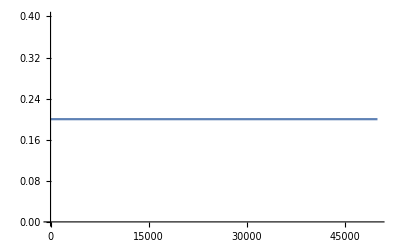

```mathematica
Plot[a[x],{x,0,50000}]
```

```mathematica
M = 1.;
Ee = 5.;
Jz = 7.;
Rinit = (4 a[0]^2-a[0]^2 Ee^2+Jz^2+√((-a[0]^2 (-4+Ee^2)+Jz^2)^2-48 (-a[0] Ee+Jz)^2 M^2))/(8 M)
```

9.0598

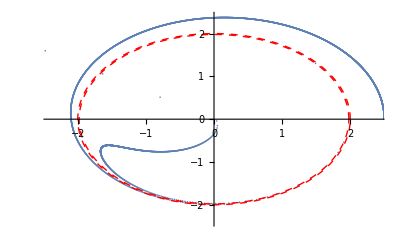

```mathematica
fnvals = RKODE4[G, 0., {2.5, 0., 0.},.001,20000];

xyplot = Table[{fnvals[[j,2,1]] Cos[fnvals[[j,2,3]]], fnvals[[j,2,1]] Sin[fnvals[[j,2,3]]]},{j,1,Length[fnvals]}];

pltrng = 2.4;

trajectory = ListPlot[{xyplot},PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->Thickness[2.]];

ergosphere = PolarPlot[{M+Sqrt[M^2-a[0]^2Cos[Pi/2]^2],M+Sqrt[M^2-a[0]^2]},{T,0,2 Pi},PlotStyle->Directive[Red,Thin,Dashed]];

Show[trajectory,ergosphere]
```

```mathematica
plotdata = Table[0,10000];
```

```mathematica
For[i=-5000,i<5000,i++,
a[x_] = i*0.0001;
spincheck = i;
fnvals = RKODE4[G, 0., {2.5, 0., 0.},.001,60000];
rkodecheck = i;
trajectory = Table[{fnvals[[j,2,1]] Cos[fnvals[[j,2,3]]], fnvals[[j,2,1]] Sin[fnvals[[j,2,3]]]},{j,1,Length[fnvals]}];
trajcheck = i;
surfaces ={M+Sqrt[M^2-2*a[0]^2Cos[Pi/2]^2],M+Sqrt[M^2-2*a[0]^2]};
surfcheck = i;

plotdata[[i]] = {trajectory,surfaces};
writecheck = i;
]
```

$Aborted

```mathematica
Dynamic["Calculated spin "<>ToString[spincheck]]
Dynamic["Integrating traj "<>ToString[rkodecheck]]
Dynamic["Calculated trajectory "<>ToString[trajcheck]]
Dynamic["Calculated surfaces "<>ToString[surfcheck]]
Dynamic["Wrote to array "<>ToString[writecheck]]1
```

```mathematica
plotdata[[1]]
```

Part::partd: Part specification plotdata ⟦ 1 ⟧ is longer than depth of object.

plotdata⟦1⟧

```mathematica
Dynamic[Dimensions[plotdata]]
```

```mathematica
m = Animate[plots[[Round[i]]],{i,-2000,2000},AnimationRate->50]
```

```mathematica
Export["changing_a.avi",m,"FrameRate"-> 30]
```